```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["/Users/jsdillon/Desktop/Joint_Mapmaking_Power_Spectrum_Pipeline/FacetedMapmaker/Test PSF Convolution/HERA PSF 1"];
PSFdata = Import["PSF.dat"];
```

```mathematica
nx = Sqrt[Length[PSFdata]];
ny = nx;
```

```mathematica
PSFtable = Table[Transpose[ArrayReshape[PSFdata⟦j+(i-1)*ny,;;⟧,{nx,ny}]],{i,1,nx,1},{j,1,ny,1}];
Manipulate[ArrayPlot[PSFtable⟦position⟦1⟧,position⟦2⟧⟧,DataReversed->True,PlotLabel->{position},FrameLabel->{"Dec Bin","RA Bin"},PlotLegends->BarLegend[All]],{{position,{Round[nx/2],Round[ny/2]}},{1,1},{nx,ny},{1,1}}]
```

```mathematica
map = Import["map.dat"];
ArrayPlot[Transpose[map],FrameLabel->{"Dec Bin","RA Bin"},DataReversed->True,PlotLabel->"Renormalized Map",ImageSize->{300,300},PlotLegends->BarLegend[All]]
```

-Graphics-

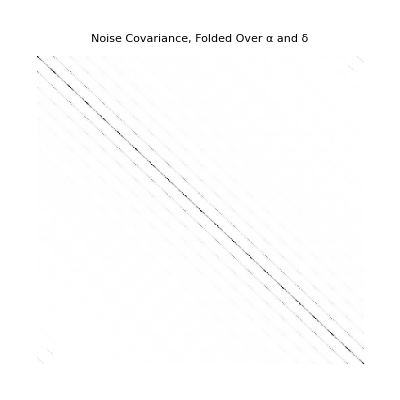

```mathematica
Ncov = Import["noiseCov.dat"];
ArrayPlot[Ncov,PlotLabel->"Noise Covariance, Folded Over α and δ"]
```

```mathematica
NVariance = Log10[Diagonal[Ncov]];
ArrayPlot[ArrayReshape[NVariance,{nx,ny}],ColorFunction->ColorData["GrayTones"],PlotRange->{Min[NVariance],Max[NVariance]},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Test =Table[Random[],{x,1,4},{y,1,4}] 
Test //MatrixForm
```

{{0.99888,0.895762,0.117985,0.163606},{0.375349,0.259032,0.978005,0.577163},{0.176141,0.583549,0.892583,0.241196},{0.595047,0.465159,0.518816,0.378498}}

(0.99888 | 0.895762 | 0.117985 | 0.163606
0.375349 | 0.259032 | 0.978005 | 0.577163
0.176141 | 0.583549 | 0.892583 | 0.241196
0.595047 | 0.465159 | 0.518816 | 0.378498)

```mathematica
Test[[;;,1]]
Test[[1,;;]]
ArrayReshape[Test[[1,;;]],{2,2}] //MatrixForm
```

{0.99888,0.375349,0.176141,0.595047}

{0.99888,0.895762,0.117985,0.163606}

(0.99888 | 0.895762
0.117985 | 0.163606)

```mathematica
PSFtable = Table[Transpose[ArrayReshape[PSFdata⟦j+(i-1)*ny,;;⟧,{nx,ny}]],{i,1,nx,1},{j,1,ny,1}];
Manipulate[ArrayPlot[PSFtable⟦position⟦1⟧,position⟦2⟧⟧,DataReversed->True,PlotLabel->{position},FrameLabel->{"Dec Bin","RA Bin"},PlotLegends->BarLegend[All]],{{position,{Round[nx/2],Round[ny/2]}},{1,1},{nx,ny},{1,1}}]
```